1.54525+0.155458 x

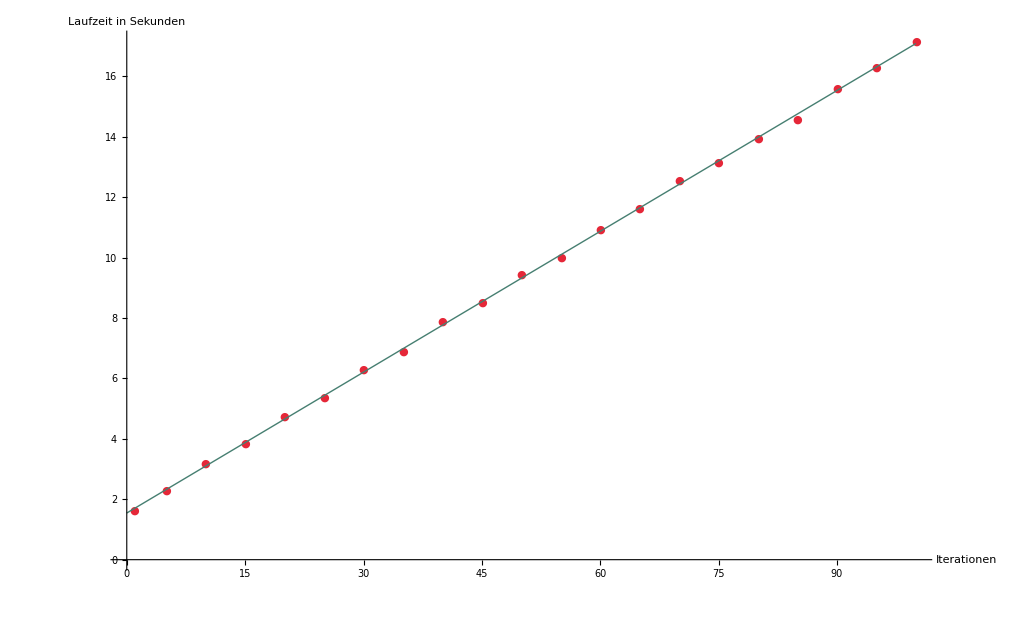

```mathematica
jacobiTimes=Import["/home/philipp/diplomarbeit/data/jacobi_time.csv","Table","FieldSeparators"->";"];
linearFunction=Fit[jacobiTimes,{1,x},x]
Show[
ListPlot[
jacobiTimes,
PlotMarkers->{Automatic,Medium},
PlotStyle->{RGBColor[229/255,39/255,56/255]},
AxesLabel->{"Iterationen","Laufzeit in Sekunden"},
LabelStyle->{FontFamily->{"sans"},FontSize->30}
],
Plot[
linearFunction,
{x,0,100},
PlotStyle->{RGBColor[70/255,127/255,113/255]}]]
```